```mathematica
Needs["ErrorBarPlots`"]
Needs["PlotLegends`"]
```

PlotLegend::shdw: Symbol PlotLegend appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

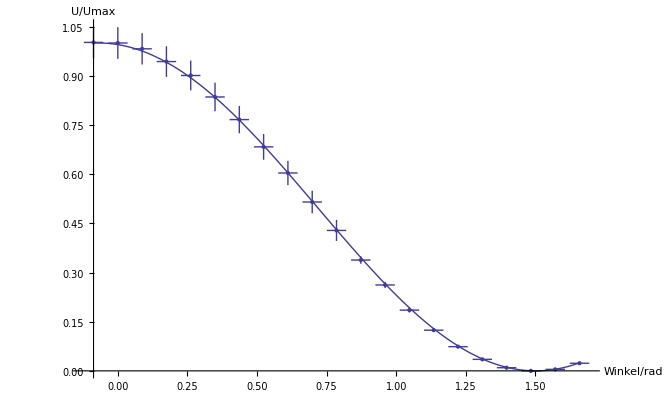

```mathematica
Imax=5.65;data1={{-5, 0, 5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 55, 60, 65, 70, 75, 80, 85, 90, 95}, {5.66, 5.65, 5.55, 5.33, 5.09, 4.72, 4.33, 3.86, 3.41, 2.91, 2.42, 1.910, 1.480, 1.047, 0.701, 0.417, 0.1983, 0.0540, 0, 0.0257, 0.1312}, {0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.01, 0.001, 0.001, 0.001, 0.001, 0.001, 0.0001, 0.0001, 0.0001, 0.0001, 0.0001}};
pdatap=Table[{{data1[[1,x]] Degree,data1[[2,x]]/Imax},ErrorBar[2/180 π,data1[[3,x]]*2+data1[[2,x]]*0.005]},{x,1,21}];

Show[ErrorListPlot[pdatap],Plot[Cos[x+4Degree]^2,{x,-5 Degree,95 Degree}],AxesOrigin->{-5Degree,0},AxesLabel->{"Winkel/rad","U/Umax"}]
```

```mathematica
data2={{0, 15, 30, 45}, {267, 299, 328, 360}, {0, 28, 60, 90}};
min=Table[{{data2[[1,x]],data2[[2,x]]-360},ErrorBar[2,2]},{x,1,4}];
max=Table[{{data2[[1,x]],data2[[3,x]]},ErrorBar[2,2]},{x,1,4}];
```

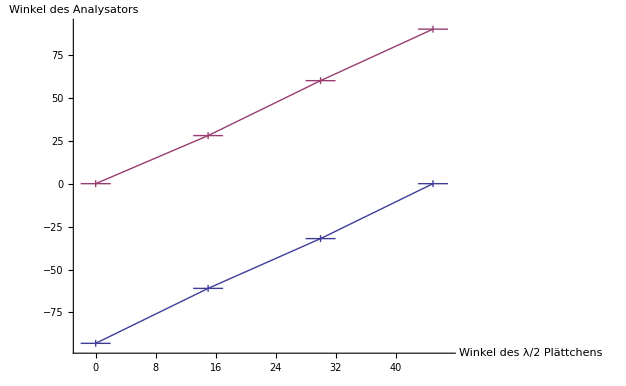

```mathematica
ErrorListPlot[{min,max},
AxesLabel->{"Winkel des λ/2 Plättchens","Winkel des Analysators"},Joined->True]
```

```mathematica
data3={{0, 10, 20, 30, 40, 50, 60, 70, 80, 90, 100, 110, 120, 130, 140, 150, 160, 170, 180}, {2.48, 2.33, 2.21, 2.13, 2.11, 2.14, 2.24, 2.40, 2.55, 2.71, 2.87, 2.99, 3.06, 3.10, 3.07, 2.97, 2.82, 2.65, 2.47}, {2.85, 3.13, 3.33, 3.44, 3.45, 3.36, 3.18, 2.95, 2.67, 2.38, 2.12, 1.90, 1.80, 1.78, 1.85, 2.03, 2.27, 2.63, 2.81}, {4.21, 4.53, 4.60, 4.43, 4.04, 3.51, 2.86, 2.18, 1.56, 1.07, 0.76, 0.67, 0.82, 1.18, 1.71, 2.35, 3.02, 3.64, 4.12}, {5.22, 5.11, 4.71, 4.04, 3.21, 2.29, 1.45, 0.74, 0.26, 0.05, 0.15, 0.54, 1.17, 2.00, 2.89, 3.76, 4.47, 4.96, 5.14}};
```

```mathematica
i45=Table[{data3[[1,x]],data3[[2,x]]},{x,1,19}];
i30=Table[{data3[[1,x]],data3[[3,x]]},{x,1,19}];
i15=Table[{data3[[1,x]],data3[[4,x]]},{x,1,19}];
i0=Table[{data3[[1,x]],data3[[5,x]]},{x,1,19}];
```

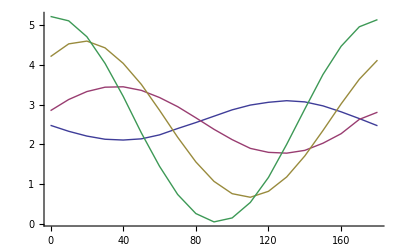

```mathematica
ListPlot[{i45,i30,i15,i0},Joined->True]
```

```mathematica
i45p=Table[{data3[[1,x]]Degree,data3[[2,x]]},{x,1,19}];
i45p2=Join[i45p , Table[{i45p[[x,1]],-i45p[[x,2]]},{x,1,19}]];
i30p=Table[{data3[[1,x]]Degree,data3[[3,x]]},{x,1,19}];
i30p2=Join[i30p , Table[{i30p[[x,1]],-i30p[[x,2]]},{x,1,19}]];
i15p=Table[{data3[[1,x]]Degree,data3[[4,x]]},{x,1,19}];
i15p2=Join[i15p , Table[{i15p[[x,1]],-i15p[[x,2]]},{x,1,19}]];
i0p=Table[{data3[[1,x]]Degree,data3[[5,x]]},{x,1,19}];
i0p2=Join[i0p , Table[{i0p[[x,1]],-i0p[[x,2]]},{x,1,19}]];
```

```mathematica
ListPolarPlot[{i0p2,i15p2,i30p2,i45p2},PlotLegend->{"0°","15°","30°","45°"},Joined->True]
```

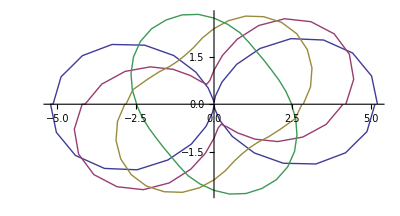

```mathematica
Manipulate[Show[ListPolarPlot[{i30p2,i45p2,i15p2,i0p2},Joined->True],PolarPlot[5.14((Cos[ψ+ξ]Cos[ϕ+γ])^2+(Sin[ψ+ξ]Sin[ϕ+δ+γ])^2),{ϕ,0,360Degree}]],{γ,0,2π},{ξ,0,40Degree},{ψ,0,2π},{δ,0,2Pi}]
```

```mathematica
(2 π-6.08212)/(2π)
```

0.0320005

```mathematica
670/4//N
```

167.5

```mathematica
3.07876/(2 π)
```

0.49